```mathematica
(* From Cano et al. 2110.11378 *)
δωp=ℓ^4/M^5(Subscript[λ, e](0.0533+0.0255I)+((0.0152-0.0556I)Subscript[λ, e]^2+(0.0139-0.0580I)Subscript[λ, o]^2)^(1/2))
δωm=ℓ^4/M^5(Subscript[λ, e](0.0533+0.0255I)-((0.0152-0.0556I)Subscript[λ, e]^2+(0.0139-0.0580I)Subscript[λ, o]^2)^(1/2))
```

(ℓ^4 ((0.0533+0.0255 ⅈ) λ_e+√((0.0152-0.0556 ⅈ) λ_e^2+(0.0139-0.058 ⅈ) λ_o^2)))/M^5

(ℓ^4 ((0.0533+0.0255 ⅈ) λ_e-√((0.0152-0.0556 ⅈ) λ_e^2+(0.0139-0.058 ⅈ) λ_o^2)))/M^5

Focus on the case λ_o = 0 for the moment.

```mathematica
Simplify[{δωp,δωm}/.{Subscript[λ, o]->0},Assumptions->Subscript[λ, e]>0]
```

{((0.244141-0.120171 ⅈ) ℓ^4 λ_e)/M^5,-((0.137541-0.171171 ⅈ) ℓ^4 λ_e)/M^5}

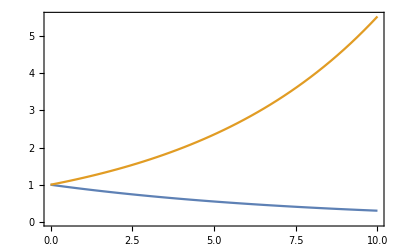

```mathematica
Plot[{Exp[-0.120 t],Exp[+0.171 t]},{t,0,10},Frame->True]
```

```mathematica
-1/11.2407
```

```mathematica
0.171/-0.08896243116531888
```

-1.92216

```mathematica
1/% (* This is δτ^(0) *)
```

-0.520248

```mathematica
-0.13754059277988612/0.3737(* This is δω^(0) *)
```

-0.368051